# Animation of squeezed-coherent state wavefunctions

## Description

In this notebook we describe a way to create movies of the squeezed-coherent state wavefunctions in position and momentum space as functions of time.

## Setting up the functions

In order to start creating your own animation you need to install LevelScheme

LevelScheme allows you to modify the length of the ticks in your plots.

Once you have installed the aforementioned package, the next three lines are used to load it (you need to add your path to the file between quotation marks)

```mathematica
AppendTo[$Path,"/yourpath/LevelScheme"];
```

```mathematica
Get["LevelScheme`"]
```

LevelScheme scientific figure preparation system
M. A. Caprio, Department of Physics, University of Notre Dame
Comput. Phys. Commun. 171, 107 (2005)
Version 3.53 (January 10, 2013)
View color paletteVisit home page  -Graphics-

```mathematica
SetOptions[LinTicks,MajorTickLength->{0.02,0},MinorTickLength->{0.013,0}];
```

## Defining the wavefunctions, uncertainties and expectation values

Start by defining the squeezed-coherent state wavefunction in position space ψTimeDep[x_,r_,ϕ_,x0_,p0_,t_] and in momentum space ΦTimeDep[p_,r_,ϕ_,x0_,p0_,t_]

In order to simplify all our expressions we will make both wavefunctions dimensionless.

First, let the dimensionless time coordinate t≡ωt’

Next, let the dimensionless position coordinate x≡√(mω/ℏ) x’ , so that x_0≡√(mω/ℏ) x_0' . Then multiply the wavefunction in position space by (ℏ/mw)^(1/4). The dimensionless wavefunction then has the following form,

```mathematica
ψTimeDep[x_,r_,ϕ_,x0_,p0_,t_]:=(1/Pi)^(1/4) * 1/Sqrt[Cosh[r] - Exp[-2*ⅈ*t]*Sinh[r]]*Exp[ⅈ*(p0*Cos[t] - x0*Sin[t])* x]*Exp[-ⅈ/(2)*(x0*Cos[t] + p0*Sin[t])*(p0*Cos[t] - x0*Sin[t])]*Exp[-1/(2)*(Cosh[r] + Exp[-2*ⅈ*t]*Sinh[r])/(Cosh[r] - Exp[-2*ⅈ*t]*Sinh[r]) * (x - (x0*Cos[t] + p0*Sin[t]))^2]
```

Next, let the dimensionless momentum coordinate p≡1/(√ℏmω)p' , so that  p_0≡ 1/(√ℏmω)p_0'  . Then multiply the wavefunction in momentum space by (ℏmω)^(1/4). The dimensionless wavefunction then has the following form,

```mathematica
ΦTimeDep[p_,r_,ϕ_,x0_,p0_,t_]:=(1/Pi)^(1/4) * 1/Sqrt[Cosh[r]+Exp[-2*ⅈ*t]*Sinh[r]]*Exp[-ⅈ*(x0*Cos[t] + p0*Sin[t])* p]*Exp[ⅈ/(2)*(x0*Cos[t] + p0*Sin[t])*(p0*Cos[t] - x0*Sin[t])]*Exp[-1/(2)*(Cosh[r] - Exp[-2*ⅈ*t]*Sinh[r])/(Cosh[r] + Exp[-2*ⅈ*t]*Sinh[r]) * (p - (p0*Cos[t] - x0*Sin[t]))^2]
```

Next, define the uncertainties in position and momentum deltaX[r_,t_] and deltaP[r_,t_], respectively, and the expectation values of position and momentum expectedX[x0_,p0_,t_] and expectedP[x0_,p0_,t_], respectively.

Since we also want dimensionless uncertainties and expectation values, we need to multiply Δx(t) by √(mω/ℏ) and Δp(t) by 1/(√ℏmω)

```mathematica
deltaX[r_,t_]:=√(1/2) √(Cosh[2*r]-Sinh[2*r]*Cos[2*t])
```

```mathematica
deltaP[r_,t_]:=√(1/2) √(Cosh[2*r]+Sinh[2*r]*Cos[2*t])
```

```mathematica
expectedX[x0_,p0_,t_]:=(x0*Cos[t] + p0*Sin[t])
```

```mathematica
expectedP[x0_,p0_,t_]:=(p0*Cos[t] - x0*Sin[t])
```

## Creating the animations

Now, create the two plots for the real parts of the wavefunctions in position and momentum space.

```mathematica
p1[r_,x0_,p0_,t_]:=Plot[Re[ψTimeDep[x,r,0,x0,p0,t]],{x,-32,32},Frame->True,PlotRange->{-0.5,0.5},PlotStyle->{Thickness[0.0042],Blue},PlotPoints->100,FrameTicks->LinTicks,FrameTicksStyle->Directive[Thick,FontSize->20],FrameStyle->Directive[Black,Thick],Prolog->{Opacity[0.5,Gray],Rectangle[{N[Re[expectedX[x0,p0,t]]]-N[deltaX[r,t]],-0.5},{N[Re[expectedX[x0,p0,t]]]+N[deltaX[r,t]],0.5}]},Epilog->{Text[Style["(a)",Black,Italic,20],Scaled[{.9,.9}]],Text[Style["Position space",Blue,20],Scaled[{.19,.1}]]},Axes->{True,False},FrameLabel->{None,Style["Re (FractionBox[ℏ, mω])ψ_(ξ, α)(x, t)", FontSize -> 25, FontFamily->Times]},ImagePadding->{{89,45},{0,30}},ImageSize->600];

p2[r_,x0_,p0_,t_]:=Plot[Re[ΦTimeDep[x,r,0,x0,p0,t]],{x,-32,32},Frame->True,PlotRange->{-0.5,0.5},PlotStyle->{Thickness[0.0042],Red},PlotPoints->100,FrameTicks->LinTicks,FrameTicksStyle->Directive[Thick,FontSize->20],FrameStyle->Directive[Black,Thick],Prolog->{Opacity[0.5,Gray],Rectangle[{N[Re[expectedP[x0,p0,t]]]-N[deltaP[r,t]],-0.5},{N[Re[expectedP[x0,p0,t]]]+N[deltaP[r,t]],0.5}]},Epilog->{Text[Style["(b)",Black,Italic,20],Scaled[{.9,.9}]],Text[Style["Momentum space",Red,20],Scaled[{.19,.1}]]},Axes->{True,False},FrameLabel->{Style["Coordinates √(mω/ℏ)x and √(1/ℏmω)p", FontSize -> 25, FontFamily->Times],Style["Re (ℏmω)^(1/4)"<>ToString[Subscript[OverTilde[ψ], ξ,α], StandardForm]<>"(p, t)", FontSize -> 25, FontFamily->Times]},ImagePadding->{{89,45},{85,0}},ImageSize->600];
```

Then, create the animation. We use r=2 , x0=3 √2 and p0=3 √2 in this example

```mathematica
animation=ParallelTable[Column[{p1[2,3*√2,3*√2,t],p2[2,3*√2,3*√2,t]},Spacings->0],{t,0,6.34,0.06}];
```

Finally, export your animation by adding your path to the file you want to save between quotation marks

```mathematica
Export["/yourpath/animationA.gif",animation,"AnimationRepetitions"->∞]
```

You can also create a snapshot of the animation at any time you want by using the following piece of code. This snapshot will be taken at time t=0.4

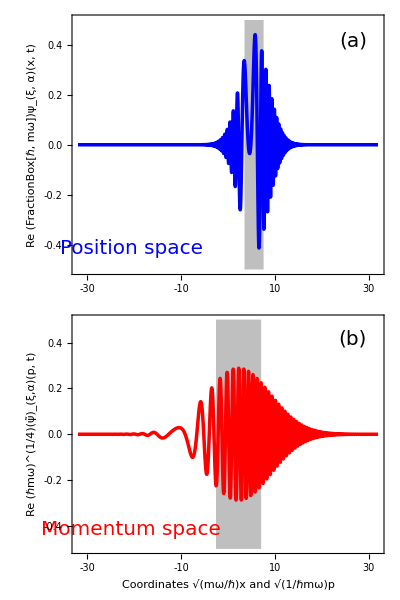

```mathematica
image1=Column[{p1[2,3*√2,3*√2,0.4],p2[2,3*√2,3*√2,0.4]},Spacings->0]
```

Then, we can export this image

```mathematica
Export["/yourpath/image.pdf",image1,"PDF",ImageSize->600]
```